## Graphical representation for the reduced inertia parameter defined in Frauendorf paper

```mathematica
ClearAll["Global`*"]
```

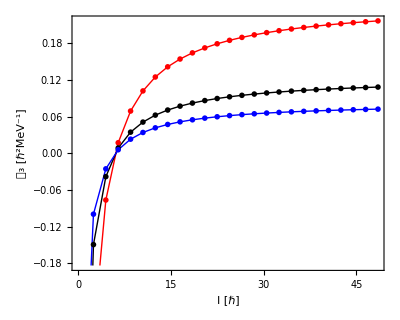

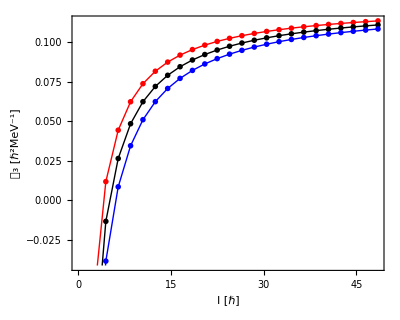

```mathematica
realspin[I_]:=Sqrt[I(I+1)];
A3reduced[A3_,I_,j_]:=A3*(1-j/realspin[I]);
plotdata[A3_,j_]:=Table[{spin,A3reduced[A3,spin,j]},{spin,1/2,50,2}];
makeplotfixedj[I3list_,j_]:=ListPlot[Table[plotdata[1/(2*I3list[[i]]),j],{i,1,Length[I3list]}],Joined->True,Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,FrameLabel->{"I [ℏ]","𝒜_3 [ℏ^2MeV^-1]"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},ImageSize->400,PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick}},PlotMarkers->"OpenMarkers"];
makeplotfixedI3[I3_,jlist_]:=ListPlot[Table[plotdata[1/(2*I3),jlist[[i]]],{i,1,Length[jlist]}],Joined->True,Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,FrameLabel->{"I [ℏ]","𝒜_3 [ℏ^2MeV^-1]"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},ImageSize->400,PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick}},PlotMarkers->"OpenMarkers"];
makeplotfixedj[{2,4,6},6.5]
makeplotfixedI3[4,{4.5,5.5,6.5}]
```